```mathematica
(*Inputs*)
g=1.5;
κ=0.2;
Get["/scratch/network/zz3250/Wolfram Mathematica/SG_SS_Kappa0p2G1p5_N50000"];
PhiVSYKappa0p2G1p5=Interpolation[FinalPhiList,InterpolationOrder->4];
ϕss[x_]:=PhiVSYKappa0p2G1p5[(π^(1/2)*Exp[(2 π*κ)^(1/2) x])/(1+Exp[(2 π*κ)^(1/2) x])];data=Table[{x,ϕss[x]},{x,-150,150,0.001}];
ϕssint=Interpolation[data];
intermediatePhi[x_]:=2*Sqrt[π]*ϕssint[x];
cosTerm[x_]:=Cos[intermediatePhi[x]];
potentialhamiltonian[x_]:=2*Pi*κ*cosTerm[x]+g^2;
```

InterpolatingFunction::dmval: Input value {1.66752×10^-73} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.66939×10^-73} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.67127×10^-73} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
L=200;
dx=.01;
total=200;
H1=-u''[x]+Evaluate[potentialhamiltonian[x]]*u[x];
{vals,fns}=NDEigensystem[{H1,DirichletCondition[u[x]==0,True]},u[x],{x,-L/2,L/2},total,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->dx}},"Arnoldi","MaxIterations"->7000,"BasisSize"->total+1,"Shift"->2.63}];
```

```mathematica
xRange=Range[-100,100,dx];
originalData=Table[{x,-fns[[1]]/. x->x},{x,xRange}];
ϕb=Interpolation[originalData];
```

```mathematica
(*Testing to find k2b*)
2*Sqrt[vals[[1]]]
Sqrt[vals[[177]]]
```

3.35569

3.35032

```mathematica
(*Setting up constants*)
k2b=177;
ωk=Sqrt[vals[[k2b]]];
tildek2b=Sqrt[ωk^2-g^2-2*Pi*κ];
λ3=2*Pi^(3/2);
λ4=4*Pi^2/3;
ωb=Sqrt[vals[[1]]];
ϕk2b=(1/Sqrt[2])*(fns[[k2b+1]]+I*fns[[k2b]]);
Vbb2b=NIntegrate[Sin[intermediatePhi[x]]*fns[[1]]*fns[[1]]*ϕk2b,{x,-100,100}];
Vbbbb=NIntegrate[Cos[intermediatePhi[x]]*fns[[1]]^4,{x,-100,100}];
```

```mathematica
Acoeff=I*λ3/(2*tildek2b*Sqrt[ωb])*Vbb2b
Bcoeff=λ3^2/(32*ωb^3)*Abs[Vbb2b]^2
Ccoeff=I*3*λ4/(8*ωb^2)*Vbbbb
```

4.36503×10^-6-0.0438842 ⅈ

0.000659976

0.-0.114787 ⅈ

```mathematica
(*I should be able to check these by making sure they align with the analytic result when λ3=0*)
myEqs={
Σ020'[t]==a010[t]*a120[t],
a010'[t]==-Bcoeff*Σ020[t]*Conjugate[a120[t]]+Ccoeff*a010[t]*(h00[t]+h10[t]),
h00'[t]==0,
h10'[t]==-Bcoeff*(a120[t]*Conjugate[Σ020[t]]*a010[t]+Conjugate[a010[t]]*Σ020[t]*Conjugate[a120[t]]),
a120'[t]==Acoeff*2*(2*ωb)^2*Conjugate[a010[t]]-Bcoeff*(Conjugate[a010[t]]*Σ020[t]+Σ130[t]*Conjugate[a230[t]])+Ccoeff*a120[t]*(h10[t]+h20[t]),
Σ130'[t]==a120[t]*a230[t],
h20'[t]==Acoeff*Conjugate[a120[t]]*Conjugate[a010[t]]-Bcoeff*(a230[t]*Conjugate[Σ130[t]]*a120[t]+Conjugate[a120[t]]*Σ130[t]*Conjugate[a230[t]]+Conjugate[Σ020[t]]*a010[t]*a120[t]+Conjugate[a120[t]]*Conjugate[a010[t]]*Σ020[t]),
a230'[t]==Acoeff*6*(2*ωb)^3*Conjugate[a120[t]]-Bcoeff*Conjugate[a120[t]]*Σ130[t]+Ccoeff*a230[t]*(h20[t]+h30[t]),
h30'[t]==Acoeff*(2*ωb)*Conjugate[a230[t]]*Conjugate[a120[t]]-Bcoeff*(Conjugate[Σ130[t]]*a120[t]*a230[t]+Conjugate[a230[t]]*Conjugate[a120[t]]*Σ130[t]),
Σ021'[t]==a011[t]*a121[t],
Σ131'[t]==a121[t]*a231[t],
a011'[t]==-Bcoeff*Σ021[t]*Conjugate[a121[t]]+Ccoeff*a011[t]*(h01[t]+h11[t]),
a121'[t]==Acoeff*Sqrt[2]*(2*ωk)*(2*ωb)^2*2*Conjugate[a011[t]]-Bcoeff*(Conjugate[a011[t]]*Σ021[t]+Σ131[t]*Conjugate[a231[t]])+Ccoeff*a121[t]*(h11[t]+h21[t]),
a231'[t]==Acoeff*Sqrt[2]*(2*ωk)*(2*ωb)^3*6*Conjugate[a121[t]]-Bcoeff*Conjugate[a121[t]]*Σ131[t]+Ccoeff*a231[t]*(h21[t]+h31[t]),
h01'[t]==Conjugate[Acoeff]*2*ωk*a010[t]*a120[t],
h11'[t]==Conjugate[Acoeff]*(2*ωb)*(2*ωk)*a120[t]*a230[t]-Bcoeff*(a121[t]*Conjugate[Σ021[t]]*a011[t]+Conjugate[a011[t]]*Σ021[t]*Conjugate[a121[t]]),
h21'[t]==Acoeff*Sqrt[2]*(2*ωk)*Conjugate[a121[t]]*Conjugate[a011[t]]-Bcoeff*(a231[t]*Conjugate[Σ131[t]]*a121[t]+Conjugate[a121[t]]*Σ131[t]*Conjugate[a231[t]]+Conjugate[Σ021[t]]*a011[t]*a121[t]+Conjugate[a121[t]]*Conjugate[a011[t]]*Σ021[t]),
h31'[t]==Acoeff*Sqrt[2]*(2*ωb)*(2*ωk)*Conjugate[a231[t]]*Conjugate[a121[t]]-Bcoeff*(Conjugate[Σ131[t]]*a121[t]*a231[t]+Conjugate[a231[t]]*Conjugate[a121[t]]*Σ131[t])
};
```

```mathematica
myIcs={Σ020[0]==0,
a010[0]==Sqrt[2*ωb],
h00[0]==1/2,
h10[0]==3*ωb,
a120[0]==(2*ωb)^(3/2),
Σ130[0]==0,
h20[0]==20*ωb^2,
a230[0]==2*(2*ωb)^(5/2),
h30[0]==21*(2*ωb)^3,
Σ021[0]==0,
Σ131[0]==0,
a011[0]==Sqrt[2*ωb]*2*ωk,
a121[0]==(2*ωb)^(3/2)*2*ωk,
a231[0]==2*(2*ωb)^(5/2)*2*ωk,
h01[0]==ωk,
h11[0]==3*ωb*2*ωk,
h21[0]==20*ωb^2*2*ωk,
h31[0]==21*(2*ωb)^3*2*ωk
};
allVars={Σ020,a010,h00,h10,a120,Σ130,h20,a230,h30,Σ021,Σ131,a011,a121,a231,h01,h11,h21,h31};
```

```mathematica
sol=NDSolve[{myEqs,myIcs},allVars,{t,0,10}][[1]]
```

{Σ020→InterpolatingFunction[{{0., 10.}}, <>],a010→InterpolatingFunction[{{0., 10.}}, <>],h00→InterpolatingFunction[{{0., 10.}}, <>],h10→InterpolatingFunction[{{0., 10.}}, <>],a120→InterpolatingFunction[{{0., 10.}}, <>],Σ130→InterpolatingFunction[{{0., 10.}}, <>],h20→InterpolatingFunction[{{0., 10.}}, <>],a230→InterpolatingFunction[{{0., 10.}}, <>],h30→InterpolatingFunction[{{0., 10.}}, <>],Σ021→InterpolatingFunction[{{0., 10.}}, <>],Σ131→InterpolatingFunction[{{0., 10.}}, <>],a011→InterpolatingFunction[{{0., 10.}}, <>],a121→InterpolatingFunction[{{0., 10.}}, <>],a231→InterpolatingFunction[{{0., 10.}}, <>],h01→InterpolatingFunction[{{0., 10.}}, <>],h11→InterpolatingFunction[{{0., 10.}}, <>],h21→InterpolatingFunction[{{0., 10.}}, <>],h31→InterpolatingFunction[{{0., 10.}}, <>]}

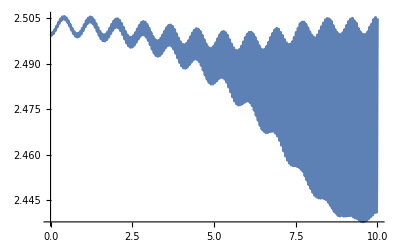

```mathematica
Plot[(Abs[h20[t]]/(8*ωb^2))/.sol,{t,0,10},PlotRange->Full]
```